# N_f=2;2πTD vs T/T_C

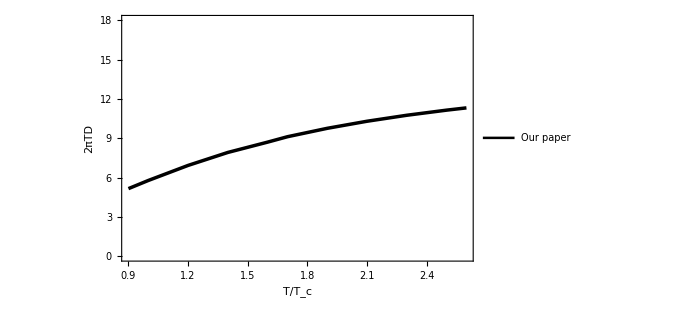

```mathematica
f1=ListLinePlot[{{0.9,5.162923184683022},{1,5.785045309749159},{1.2,6.931961440341872},{1.4,7.92057246835887},{1.6,8.70667635441106},{1.7,9.119157589078196},{1.9,9.75915177530323},{2.1,10.297739500000628},{2.3,10.753910758313273},{2.5,11.143181648519793},{2.6,11.316711060925234}},Frame->True,PlotStyle->{{Black,Thickness[0.005]}},BaseStyle->{FontFamily->"Times New Roman",FontSize->16},PlotRange->{{0.9,2.6},{0,18}},PlotLegends->Placed[LineLegend[{"Our paper"},LabelStyle->{FontSize->15}],{0.2,0.9}],FrameLabel->{Style["T/\!\(\*SubscriptBox[\(T\), \(c\)]\)",15,Black,Italic,FontFamily->"Times New Roman"],Style["2πTD",15,Black,Italic,FontFamily->"Times New Roman"]},FrameStyle->Directive[FontFamily->"Times New Roman",FontSize->16],ImageSize->{500,300}]
```

# N_f=0 Lattice;2πTD vs T/T_C

```mathematica
data1={{1.10148148148148,Around[4.45810055865922,2.11173184357542]},{1.20222222222222,Around[4.77094972067039,1.1731843575419]},{1.50024691358025,Around[4.41899441340782,1.0167597765363094]},{1.99975308641975,Around[9.03351955307263,3.5586592178771]},{2.49925925925926,Around[9.97206703910615,3.9497206703910708]}}
```

{{1.10148,4.52.1},{1.20222,4.81.2},{1.50025,4.41.0},{1.99975,9.4.},{2.49926,10.4.}}

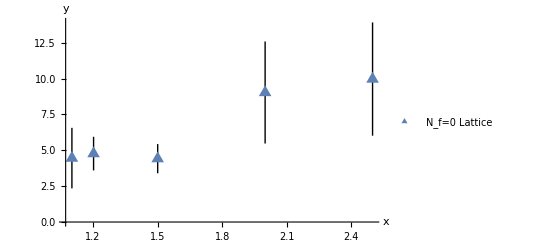

```mathematica
f5=ListPlot[data1,PlotRange->All,PlotMarkers->{"▲",15},IntervalMarkers->"Fences",IntervalMarkersStyle->{Black,"FenceWidth"->0.1,"FenceStyle"->AbsoluteThickness[1]},AxesLabel->{"x","y"},LabelStyle->{FontSize->15},PlotLegends->Placed[{"N_f=0 Lattice"},{0.5,0.9}]]
```

# N_f=2+1 Lattice;2πTD vs T/T_C

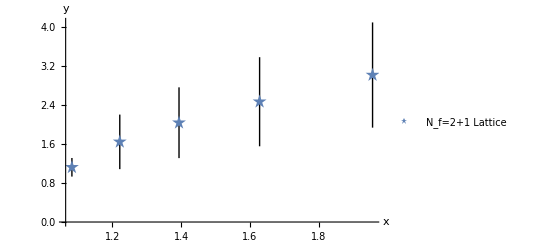

1.0777

```mathematica
data2={{1.083,Around[1.1212,0.1904]},{1.222,Around[1.642,0.5587]},{1.394,Around[2.034,0.725]},{1.628,Around[2.464,0.9126]},{1.956,Around[3.011,1.0777]}};
f6=ListPlot[data2,PlotRange->All,PlotMarkers->{"★",15},IntervalMarkers->"Fences",IntervalMarkersStyle->{Black,"FenceWidth"->0.1,"FenceStyle"->AbsoluteThickness[1]},AxesLabel->{"x","y"},LabelStyle->{FontSize->15},PlotLegends->Placed[{"N_f=2+1 Lattice"},{0.5,0.8}]]
```

# 总

```mathematica
Show[f1,f5,f6,ImageSize->{500,300}]
```